Solve::ifun: Solve 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

-Tan[π/4+Log[x]]/x

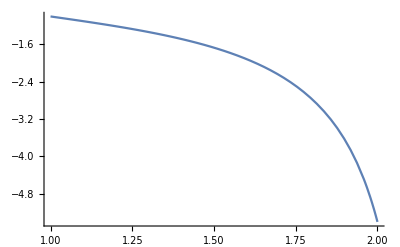

```mathematica
sol=DSolveValue[{y'[x]==-1/x^2-y[x]/x-y[x]^2,y[1]==-1},y[x],x]
Plot[Evaluate[sol],{x,1,2}]
```